### 3.5 Rules Depending on a Single Binary Relation

There are 73 inequivalent left-connected 1_2 → 2_2 rules, but none lead to structures more complex than trees. Starting each from a single self-loop, the results after 5 steps are (note that even a connected rule like {{x,y}}→{{x,z},{z,x}} can give a disconnected result):

```mathematica
GraphicsGrid[Partition[With[{ru=ResourceFunction["EnumerateWolframModelRules"][{{1,2}}->{{2,2}}]},ParallelMap[ResourceFunction["WolframModelPlot"][ResourceFunction["WolframModel"][#,{{0,0}},5,"FinalState"],ImageSize->Tiny]&,ru]],UpTo[13]],ImageSize->Full]
```

-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-
-Graphics-

With an initial condition consisting of a square graph, the following very similar results are obtained:

```mathematica
GraphicsGrid[Partition[With[{ru=ResourceFunction["EnumerateWolframModelRules"][{{1,2}}->{{2,2}}]},ParallelMap[ResourceFunction["WolframModelPlot"][ResourceFunction["WolframModel"][#,{{1,2},{2,3},{3,4},{4,1}},5,"FinalState"],ImageSize->Tiny]&,ru]],UpTo[13]],ImageSize->Full]
```

-Graphics-

There are 506 inequivalent left-connected 1_2 → 3_2 rules. Running all these rules for 5 steps starting from a single self-loop, and keeping only distinct connected results, one gets (note that similar-looking results can differ in small-scale details):

```mathematica
Module[{rules=ResourceFunction["EnumerateWolframModelRules"][{{1,2}}->{{3,2}}],res},res=ParallelMap[ResourceFunction["WolframModel"][#,{{0,0}},5,"FinalState"]&,rules];GraphicsGrid[Partition[ResourceFunction["WolframModelPlot"]/@DeleteDuplicates[Select[res,ConnectedGraphQ[Graph[UndirectedEdge@@@#]]&]],UpTo[15]],ImageSize->Full]]
```

-Graphics-

Several distinct classes of behavior are visible. Beyond simple lines, loops, trees and radial “bursts”, there are nested (“cactus-like”) graphs such as

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->180]&/@ResourceFunction["WolframModel"][{{x,y}}->{{x,z},{y,z},{z,z}},{{1,1}},5,"StatesList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

obtained from the rule

```mathematica
{{x,y}}->{{z,z},{x,z},{y,z}}
```

{{x, y}} → {{z, z}, {x, z}, {y, z}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{z,z},{x,z},{y,z}}]]
```

-Graphics-

The only slightly different rule

```mathematica
{{x,y}}->{{x,x},{x,y},{z,x}}
```

{{x, y}} → {{x, x}, {x, y}, {z, x}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{x,x},{x,y},{z,x}}]]
```

-Graphics-

gives a rather different structure:

```mathematica
ResourceFunction["WolframModel"][{{x,y}}->{{x,x},{x,y},{z,x}},{{1,1}},5,"StatesPlotsList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

A layered rendering makes the behavior slightly clearer:

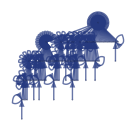
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
LayeredGraphPlot[Graph[Rule@@@#],Bottom,AspectRatio->1,VertexStyle-> ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph","VertexStyle"],
EdgeStyle-> ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph","EdgeLineStyle"]]&/@ResourceFunction["WolframModel"][{{x,y}}->{{x,x},{x,y},{z,x}},{{1,1}},5,"StatesList"]
```

Another notable rule similar to one we saw in the previous section is:

```mathematica
{{x,y}}->{{x,z},{x,z},{z,y}}
```

{{x, y}} → {{x, z}, {x, z}, {z, y}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{x,z},{x,z},{z,y}}]]
```

-Graphics-

From a single edge this gives:

```mathematica
ResourceFunction["WolframModel"][{{x,y}}->{{x,z},{x,z},{z,y}},{{1,2}},5,"StatesPlotsList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Starting from a single self-loop gives a more complex topological structure (and copies of this structure appear when the initial condition is more complex):

```mathematica
ResourceFunction["WolframModel"][{{x,y}}->{{x,z},{x,z},{z,y}},{{1,1}},5]["StatesPlotsList","MaxImageSize"->180]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

Another notable 1_2 → 2_2 rule is:

```mathematica
{{x,y}}->{{x,y},{y,z},{z,x}}
```

{{x, y}} → {{x, y}, {y, z}, {z, x}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{x,y},{y,z},{z,x}}]]
```

-Graphics-

which produces an elaborately filled-in structure:

```mathematica
ResourceFunction["WolframModel"][{{x,y}}->{{x,y},{y,z},{z,x}},{{1,1}},5]["StatesPlotsList","MaxImageSize"->180]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

After 8 steps, the structure has the form:

```mathematica
GraphPlot[Rule@@@ResourceFunction["WolframModel"][{{x,y}}->{{x,y},{y,z},{z,x}},{{1,1}},8,"FinalState"],VertexStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph","VertexStyle"],EdgeStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph","EdgeLineStyle"]]
```

-Graphics-

After t steps, there are 3^(t–1) nodes, and 1/6(3^t + 1) edges. The graph diameter is 2t – 1 if directions of edges are taken into account, and t – 1 if they are not. The maximum degree of any vertex is 2^t—and all vertices have degrees of the form 2^s, with the number of vertices of degree 2^s being proportional to 3^(t–s).

Starting from a single edge makes it slightly easier to understand what is going on:

```mathematica
ResourceFunction["WolframModel"][{{x,y}}->{{x,y},{y,z},{z,x}},{{1,2}},5,"StatesPlotsList"]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

As the rule indicates, every edge of every triangle “sprouts” a new triangle at every step, in effect producing a sequence of “frills upon frills”. But even though this may seem complicated, the whole structure basically corresponds just to a ternary tree in which each node is replaced by a triangle:

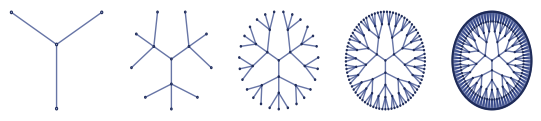

```mathematica
GraphicsRow[Table[TreePlot[KaryTree[Sum[3^i,{i,0,n}],3,VertexStyle-> ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph","VertexStyle"],
EdgeStyle-> ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph","EdgeLineStyle"]],Center],{n,1,5}]]
```

Starting from a single self loop, all 1_2 → 3_2 rules give after n steps a number of relations that is either constant, or goes like 2t – 1, 2^t – 1 or 3^(t–1).

For 1_2 → 4_2, there are 3740 distinct left-connected rules. As suggested by the random cases below, their behavior is typically similar to 1_2 → 3_2 rules, though the forms obtained can be somewhat more elaborate:

```mathematica
(*https://www.wolframcloud.com/obj/wolframphysics/TechPaper-Programs/Section-03/12-42c.wl*)
CloudGet["https://wolfr.am/KWZib4Im"]
```

-Graphics-

For example, the rule

```mathematica
{{x,y}}->{{y,z},{y,z},{z,y},{z,x}}
```

{{x, y}} → {{y, z}, {y, z}, {z, y}, {z, x}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{y,z},{y,z},{z,y},{z,x}}]]
```

-Graphics-

gives the following:

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][{{x,y}}->{{y,z},{y,z},{z,y},{z,x}},{{0,0}},5,"StatesList"]
```

-Graphics-

The rule

```mathematica
{{x,y}}->{{z,w},{w,z},{z,x},{z,y}}
```

{{x, y}} → {{z, w}, {w, z}, {z, x}, {z, y}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{z,w},{w,z},{z,x},{z,y}}]]
```

-Graphics-

gives a nested form:

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][{{1,2}}->{{3,4},{4,3},{3,1},{3,2}},{{0,0}},5,"StatesList"]
```

-Graphics-

```mathematica
ResourceFunction["WolframModel"][{{x,y}}->{{z,w},{w,z},{z,x},{z,y}},{{0,0}},6,"FinalStatePlot"]
```

-Graphics-

The rule

```mathematica
{{x,y}}->{{y,z},{y,w},{z,w},{z,x}}
```

{{x, y}} → {{y, z}, {y, w}, {z, w}, {z, x}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{y,z},{y,w},{z,w},{z,x}}]]
```

-Graphics-

gives

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][{{x,y}}->{{y,z},{y,w},{z,w},{z,x}},{{0,0}},5,"StatesList"]
```

-Graphics-

```mathematica
ResourceFunction["WolframModel"][{{x,y}}->{{y,z},{y,w},{z,w},{z,x}},{{0,0}},6,"FinalStatePlot"]
```

-Graphics-

while the similar rule

```mathematica
{{x,y}}->{{x,z},{x,w},{z,w},{z,y}}
```

{{x, y}} → {{x, z}, {x, w}, {z, w}, {z, y}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{x,z},{x,w},{z,w},{z,y}}]]
```

-Graphics-

gives

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][{{x,y}}->{{x,z},{x,w},{z,w},{z,y}},{{0,0}},5,"StatesList"]
```

-Graphics-

```mathematica
ResourceFunction["WolframModel"][{{x,y}}->{{x,z},{x,w},{z,w},{z,y}},{{0,0}},6,"FinalStatePlot"]
```

-Graphics-

Successive steps in effect just fill in this shape, which seems somewhat irregular when rendered in 2D, but appears more regular if rendered in 3D.

Another rule with a simple structure when rendered in 3D is

```mathematica
{{x,y}}->{{y,z},{y,z},{z,x},{z,x}}
```

{{x, y}} → {{y, z}, {y, z}, {z, x}, {z, x}}

```mathematica
RulePlot[ResourceFunction["WolframModel"][{{x,y}}->{{y,z},{y,z},{z,x},{z,x}}]]
```

-Graphics-

which yields:

```mathematica
ResourceFunction["WolframModelPlot"][#,"MaxImageSize"->100]&/@ResourceFunction["WolframModel"][{{1,2}}->{{2,3},{2,3},{3,1},{3,1}},{{0,0}},5,"StatesList"]
```

-Graphics-

```mathematica
GraphPlot3D[Rule@@@ResourceFunction["WolframModel"][{{1,2}}->{{2,3},{2,3},{3,1},{3,1}},{{0,0}},5,"FinalState"],VertexStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph3D","VertexStyle"],EdgeStyle->ResourceFunction["WolframPhysicsProjectStyleData"]["SpatialGraph3D","EdgeLineStyle"]]
```

The outputs from 1_2 → 4_2 rules all grow either linearly (for example, like 3t – 2), or exponentially, asymptotically like 2^t, 3^t or 4^t. The number of relations after t steps is always given by a linear recurrence relation; for the rule {{x,x}}→{{x,x},{x,x},{x,y},{x,y}} the recurrence is f[t]=3f[t–1]–2f[t–2] (with f[1]=1, f[2]=4), giving size 1/2(3 2^t – 4).